# b = 2 LRW Fractal Dimension on 3d square Lattice

## myMantissaExponent[]

```mathematica
myMantissaExponent[expr_]:=Module[{mant,exp},
{mant,exp}=MantissaExponent[expr];
mant*=10;exp-=1;
{mant,exp}
]
```

## With all the points from the CLUSTER: “b=2.000000-LRW-3d-square-lattice-data-3-201.csv” TO 401 almost

### Raw data

```mathematica
data1=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b2LRW\\b=2.000000-LRW-3d-square-lattice-data-3-201.csv"}],"CSV"],2];
```

```mathematica
data2=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b2LRW\\b=2.000000-LRW-3d-square-lattice-data-203-301.csv"}],"CSV"],2];
```

```mathematica
data3=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b2LRW\\b=2.000000-LRW-3d-square-lattice-data-303-401.csv"}],"CSV"],2];
```

```mathematica
joinedData=Join[data1,data2,data3];
```

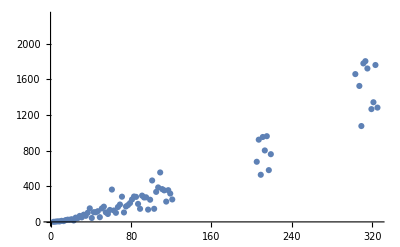

```mathematica
ListPlot[joinedData]
```

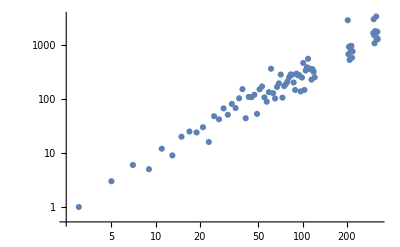

```mathematica
ListLogLogPlot[joinedData]
```

```mathematica
Clear[x]
```

```mathematica
FindFit[Log[joinedData],a+df *x,{a,df},x]
```

{a→-1.2748,df→1.51145}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x]
```

FittedModel[…]

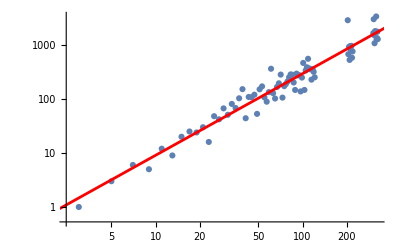

d_f=1.51145
Result from the litterature: UNKOWN

```mathematica
Show[ListLogLogPlot[joinedData],
Plot[lm[x],{x,0,1000},PlotStyle->Red]
]
Print[ "d_f=",df/.FindFit[Log[joinedData],a+df *x,{a,df},x],"
Result from the litterature: UNKOWN"]
```

```mathematica
lm["ParameterErrors"]
```

{0.177326,0.0399351}

### Drop the first few

```mathematica
dropped=Drop[joinedData,6];
lm=LinearModelFit[Log[dropped],x,x]
```

FittedModel[…]

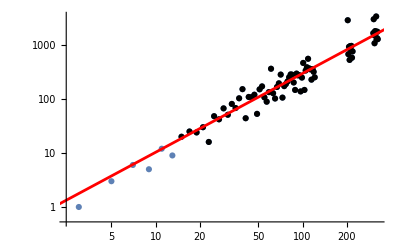

d_f=1.45959
Result from the litterature: UNKNOWN

```mathematica
Show[ListLogLogPlot[joinedData],ListLogLogPlot[dropped,PlotStyle->Black],
Plot[lm[x],{x,0,1000},PlotStyle->Red]
]
Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"
Result from the litterature: UNKNOWN"]
```

### Get stdDev by using Kay’s method

#### All the data

```mathematica
rawData=joinedData;
```

```mathematica
empirical=Module[{sampled,lm,a,df,x,slopeData,meanSlope,stdDevSlope},

slopeData=Table[
sampled=RandomSample[Log[joinedData],Floor[Length[joinedData]/2]];

lm=FindFit[sampled,a+df *x,{a,df},x];

df/.lm
,{i,1,10000}];

meanSlope=Mean[slopeData];
stdDevSlope=StandardDeviation [slopeData];

Return[{meanSlope,stdDevSlope}];
];
```

Return[{1.50888,0.0394233}]

```mathematica
empirical
```

{1.50888,0.0394233}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x];
lm["ParameterErrors"]
{meanExact,stdDevExact}={(lm["ParameterTable"]//Normal)[[1,3,2]],lm["ParameterErrors"][[2]]}
dfExact=df/.FindFit[joinedData,a+df *x,{a,df},x]
{mantExact,expExact}=myMantissaExponent[meanExact]
{mantstdDevExact,expstdDevExact}=MantissaExponent[stdDevExact]
```

{0.177326,0.0399351}

{1.51145,0.0399351}

6.00932

{1.51145,0}

{0.399351,-1}

```mathematica
{mantEmp,expEmp}=myMantissaExponent[empirical[[1]]]
```

{1.50888,0}

```mathematica
Print[" The exact value of the slope from the data is (",mantExact,"±",mantstdDevExact,")×",Superscript[10,MantissaExponent[meanExact][[2]]-1], "
 While, by using Kay's procedure, we get (",mantEmp,"±",MantissaExponent[empirical[[2]]][[1]],")×",Superscript[10,expEmp]]
```

The exact value of the slope from the data is (1.51145±0.399351)×10^0
 While, by using Kay's procedure, we get (1.50888±0.394233)×10^0

#### On dropped data

```mathematica
joinedData=dropped=Drop[rawData,6];
```

```mathematica
empirical=Module[{sampled,lm,a,df,x,slopeData,meanSlope,stdDevSlope},

slopeData=Table[
sampled=RandomSample[Log[joinedData],Floor[Length[joinedData]/2]];

lm=FindFit[sampled,a+df *x,{a,df},x];

df/.lm
,{i,1,10000}];

meanSlope=Mean[slopeData];
stdDevSlope=StandardDeviation [slopeData];

Return[{meanSlope,stdDevSlope}];
];
```

Return[{1.45894,0.0521514}]

```mathematica
empirical
```

{1.45894,0.0521514}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x];
lm["ParameterErrors"]
{meanExact,stdDevExact}={(lm["ParameterTable"]//Normal)[[1,3,2]],lm["ParameterErrors"][[2]]}
dfExact=df/.FindFit[joinedData,a+df *x,{a,df},x]
{mantExact,expExact}=myMantissaExponent[meanExact]
{mantstdDevExact,expstdDevExact}=MantissaExponent[stdDevExact]
```

{0.241707,0.0527897}

{1.45959,0.0527897}

6.15788

{1.45959,0}

{0.527897,-1}

```mathematica
{mantEmp,expEmp}=myMantissaExponent[empirical[[1]]]
```

{1.45894,0}

```mathematica
Print[" The exact value of the slope from the data is (",mantExact,"±",mantstdDevExact,")×",Superscript[10,MantissaExponent[meanExact][[2]]-1], "
 While, by using Kay's procedure, we get (",mantEmp,"±",MantissaExponent[empirical[[2]]][[1]],")×",Superscript[10,expEmp]]
```

The exact value of the slope from the data is (1.45959±0.527897)×10^0
 While, by using Kay's procedure, we get (1.45894±0.521514)×10^0